## Application to Differential Equations

One application of the variational principle is computation of approximate solutions to differential equations.

### Example: f''(x)+f(x)+x==0

Consider the differential equation f''(x)+f(x)+x==0 with boundary conditions f(0)==f(1)==0.

In this simple example, direct solution is not difficult:

```mathematica
DSolve[{f''(x)+f(x)+x==0,f(0)==f(1)==0},f(x),x]
```

{{f(x)→csc(1) sin(x)-x}}

### Variational formulation

It is easy to confirm that, for the functional

```mathematica
ℱ[f_,x_]:=1/2 (f'(x))^2-1/2(f(x))^2-x f(x);
```

the Euler-Lagrange equation reads

```mathematica
(∂ℱ[f,x])/(∂f(x))-Subscript[ⅆ, x](∂ℱ[f,x])/(∂f'(x))==0
```

-f''(x)-f(x)-x==0

which is just the (negative of the) original differential equation.

So, instead of solving the differential equation, we can compute the stationary solution of the functional

ℐ[f]==∫_0^1 (1/2(f'(x))^2-1/2(f(x))^2-x f(x))ⅆx.

### Approximate variational solution

To solve this equation approximately, guess a trial function that

Satisfies the boundary conditions;

Looks qualitatively like the expected solution;

Leads to reasonably simple evaluation of the functional ℐ[f].

A simple function that satisfies the boundary conditions y(0)==y(1)==0 is the quadratic

```mathematica
Subscript[f, α_](x_):=α x (1-x)
```

where α is arbitrary. The functional

```mathematica
ℐ[f_]:=∫_0^1 (1/2(f'(x))^2-1/2(f(x))^2-x f(x))ⅆx
```

evaluates to

```mathematica
ℐ[Subscript[f, α]]
```

(3 α^2)/20-α/12

for our simple quadratic function f_α.

Determine the stationary value of the functional leads to the optimum value of α:

```mathematica
sol=Solve[D[ℐ[Subscript[f, α]], α]==0,α]
```

{{α→5/18}}

Compare the exact solution and approximate (variational) solution:

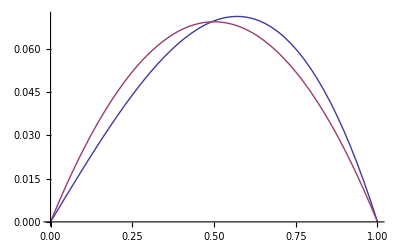

```mathematica
Plot[{Tooltip[csc(1) sin(x)-x,"exact"],Tooltip[Subscript[f, α](x)/.sol,"variational"]},{x,0,1}]
```

### Variational Solution to ODE

***This needs to be reorganised and re-worked...

Consider the following simple linear differential equation

f''(x)-x f(x)==x

with boundary conditions

f(0)==f(1)==0 .

Compute and plot the exact solution to this differential equation. [2 Marks]

Note that the solution is not simple. Nevertheless you can still evaluate it numerically or plot it.

Consider

ℱ≡ℱ[f,f',x]=1/2 (f'(x))^2+1/2 x (f(x))^2+x f(x).

Show that the Euler-Lagrange equation (∂ℱ)/(∂f(x))-ⅆ_x(∂ℱ)/(∂f'(x))==0 yields the differential equation (DisplayFormulaNumbered). [2 Marks]

Now consider the functional

ℐ[f]=∫_0^1 ℱ[f,f',x]ⅆx≡∫_0^1 (1/2 (f'(x))^2+1/2 x (f(x))^2+x f(x))ⅆx

for an arbitrary (integrable) function f. A simple function, with one variational parameter α, is

```mathematica
Subscript[f, α_](x_):=α x (1-x)
```

Check that f_α(x) satisfies the boundary conditions y(0)==y(1)==0. [1 Mark]

Plot the exact solution along with f_α(x) for various values of α using Manipulate and estimate the optimal value for α. [1 Mark]

Compute the stationary value of the functional ℐ[f_α(x)] to obtain the optimum value of α. Plot the exact solution and the approximate (variational) solution together. [2 Marks]

Next, consider a more general function with two variational parameters, α and β,

```mathematica
Subscript[f, α_,β_](x_):=x (1-x) (α+β x)
```

Check that f_(α,β)(x) satisfies the boundary conditions y(0)==y(1)==0. [1 Mark]

Compute the stationary value of the functional ℐ[f_(α,β)(x)] to obtain the optimum values of α and β. [1 Mark]

Plot the exact solution and the approximate (variational) solution together. [1 Mark]

#### Solution

### Solution to the differential equation

The solution to this differential equation is rather complicated, involving Airy functions:

```mathematica
de=f''(x)-x f(x)==x;
```

```mathematica
bcs=f(0)==f(1)==0;
```

The solution is not simple:

```mathematica
dsol=First@DSolve[Join[{de,bcs}],f,x]//Simplify
```

{f→({x}↦1/(1/3 (√3 1-1))(-2 3^(1/6) π 1 x+2 3^(1/6) π 1 x-√3 π 1/3 1 x x+√3 π 1/3 1 1 x-π 1/3 1 x x+π 1/3 1 1 x-√3 π 1/3 1 1 x+√3 π 1/3 1 x x+π 1/3 1 x x-π 1/3 1 1 x))}

Nevertheless you can still evaluate it numerically and plot it:

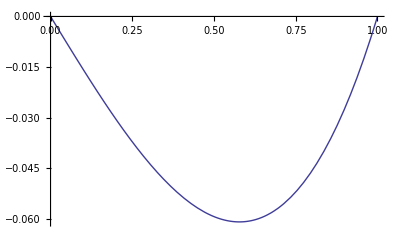

```mathematica
Plot[Evaluate[f(x)/.dsol],{x,0,1}]
```

### Euler-Lagrange equation

With

```mathematica
ℱ[f_,x_]:=1/2 (f'(x))^2+1/2 x (f(x))^2+x f(x);
```

the  Euler-Lagrange equation yields the given differential equation:

```mathematica
(∂ℱ[f,x])/(∂f(x))-Subscript[ⅆ, x](∂ℱ[f,x])/(∂f'(x))==0
```

-f''(x)+x f(x)+x==0

```mathematica
%==de//FullSimplify
```

True

### One parameter

f_α(x) satisfies the boundary conditions y(0)==y(1)==0:

```mathematica
Subscript[f, α](0)==Subscript[f, α](1)==0
```

True

The functional is

```mathematica
ℐ[f_]:=∫_0^1 (1/2 (f'(x))^2+1/2 x (f(x))^2+x f(x))ⅆx
```

An estimate for the optimal value of the parameter α is ≈-0.24.

```mathematica
Manipulate[Plot[Evaluate[{Tooltip[f[x]/.dsol,"Exact"],Tooltip[Subscript[f, α][x],"Variational"]}],{x,0,1},PlotRange->{-0.13,0}],{α,-0.5,-0.1},SaveDefinitions->True]
```

Evaluate the functional integral.

```mathematica
ℐ[Subscript[f, α]]
```

(7 α^2)/40+α/12

leading to the following optimal value for α.

```mathematica
sol=Solve[D[ℐ[Subscript[f, α]], α]==0,α]
```

{{α→-5/21}}

Compare the exact solution and approximate (variational) solution:

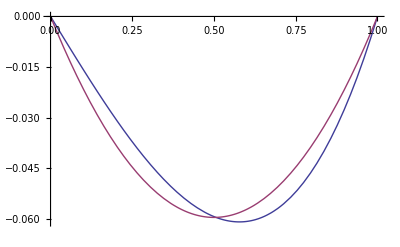

```mathematica
Plot[Evaluate[{Tooltip[f[x]/.dsol,"Exact"],Tooltip[Subscript[f, α][x]/.sol,"Variational"]}],{x,0,1}]
```

### Two parameters

Next try

```mathematica
Subscript[f, α_,β_](x_):=x (1-x)(α+β x)
```

Check the boundary conditions:

```mathematica
Subscript[f, α,β](0)==Subscript[f, α,β](1)==0
```

True

The functional integral becomes

```mathematica
ℐ[Subscript[f, α,β]]
```

(7 α^2)/40+(37 α β)/210+α/12+(39 β^2)/560+β/20

leading to the following optimal values for α and β

```mathematica
sol2=First@Solve[{D[ℐ[Subscript[f, α,β]], α]==0,D[ℐ[Subscript[f, α,β]], β]==0},{α,β}]//Simplify
```

{α→-987/6247,β→-994/6247}

The variational solution is quite simple.

```mathematica
Factor[Subscript[f, α,β](x)/.sol2]
```

(7 (x-1) x (142 x+141))/6247

Compare the exact solution and approximate (variational) solution:

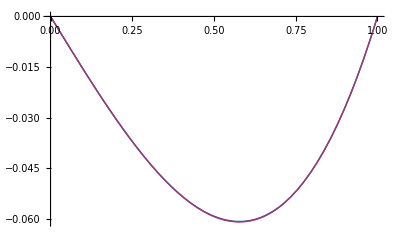

```mathematica
Plot[Evaluate[{Tooltip[f[x]/.dsol,"Exact"],Tooltip[Subscript[f, α,β][x]/.sol2,"Variational"]}],{x,0,1}]
```

The agreement is very good.